```mathematica
Clear[Γ]
```

```mathematica
G[z_+1]:=Γ[z]G[z]
G[w_ (z_ + y_)]:=G[w z + w y]
Γ[w_ (z_ + y_)]:=Γ[w z + w y]
```

```mathematica
G[z_+1]:=Γ[z]G[z]
G[z_+2]:=Γ[z+1]G[z+1]
G[z_+3]:=Γ[z+2]G[z+2]
G[z_+4]:=Γ[z+3]G[z+3]
G[z_-1]:=G[z]/Γ[z-1]
G[z_-2]:=G[z-1]/Γ[z-2]
G[z_-3]:=G[z-2]/Γ[z-3]
G[z_-4]:=G[z-3]/Γ[z-4]
G[w_ (z_ + y_)]:=G[w z + w y]
Γ[z_+1]:=z Γ[z]
Γ[z_+2]:=(z+1)Γ[z+1]
Γ[z_+3]:=(z+2)Γ[z+2]
Γ[z_+4]:=(z+3)Γ[z+3]
Γ[z_-1]:=Γ[z]/(z-1)
Γ[z_-2]:=Γ[z-1]/(z-2)
Γ[z_-3]:=Γ[z-2]/(z-3)
Γ[z_-4]:=Γ[z-3]/(z-4)
Γ[w_ (z_ + y_)]:=Γ[w z + w y]
```

```mathematica
A3Roots= Flatten[Table[If[a+b+c==0&&(a^2+b^2+c^2==2),{a,b,c},Nothing],{a,-1,1},{b,-1,1},{c,-1,1}],2];
A3Lattice = Flatten[Table[If[a+b+c==0,{a,b,c},Nothing],{a,-3,3},{b,-3,3},{c,-3,3}],2];
Z3Lattice = Flatten[Table[{a,b,c},{a,-2,2},{b,-2,2},{c,-2,2}],2];
λ1=1/4{1,0,0}-1/4{1,1,1};
λ2=1/4{1,1,0}-2/4{1,1,1};
λ3=1/4{1,1,1}-3/4{1,1,1};
σ={σ1,σ2,σ3};
F[v1_,v2_,v3_]:=1/(Product[If[a.{v1,v2,v3}==1,Abs[(-a.σ)]//Refine,1]If[a.{v1,v2,v3}==2,(-a.σ)^2(1+a.σ)^2,1]If[a.{v1,v2,v3}==3,(Abs[(-a.σ)]//Refine)(-a.σ)^2(a.σ+1)^4(a.σ+2)^2,1]If[a.{v1,v2,v3}==4,(-a.σ)^4(a.σ+1)^6(a.σ+2)^4(a.σ+3)^2,1]If[a.{v1,v2,v3}==5,(Abs[(-a.σ)]//Refine)(-a.σ)^4(a.σ+1)^8(a.σ+2)^6(a.σ+3)^4(a.σ+4)^2,1],{a,A3Roots}])//Cancel
F[{v1_,v2_,v3_}]:=F[v1,v2,v3]
$Assumptions=1>σ1>σ2>σ3>0&&ϵ>0;
```

```mathematica
f[x_]:=ⅇ^((3 x^2)/2) x^(x^2/2)//Simplify
g[x_]:=1/(G[1+x]G[1-x])//Cancel
f[x_]:=ⅇ^(-1/6-1/(528 x^8)+1/(720 x^6)-1/(504 x^4)+1/(120 x^2)+3/2  x^2) Glaisher^2 x^(1/6-x^2)//Simplify
(*f[x_]:=ⅇ^(-1/6-77683/(2760 x^20)+174611/(59400 x^18)-43867/(114912 x^16)+3617/(57120 x^14)-1/(72 x^12)+691/(163800 x^10)-1/(264 x^8)+1/(720 x^6)-1/(504 x^4)+1/(120 x^2)+3/2  x^2) Glaisher^2 x^(1/6-x^2)//Simplify
f[x_]:=ⅇ^(-1/6+3/2  x^2) Glaisher^2 x^(1/6-x^2)//Simplify*)
f[x_]:=ⅇ^(-1/(504 x^4)+1/(120 x^2)+3/2  x^2) Glaisher^2 x^(-x^2)//Simplify

f[x_]:=ⅇ^(-1/6-1/(528 x^8)+1/(720 x^6)-1/(504 x^4)+1/(120 x^2)+3/2  x^2) Glaisher^2 x^(1/6-x^2)//Simplify
f2[σ1_,σ2_,σ3_]:=f[σ1-σ2]f[σ1-σ3]f[σ2-σ3]//Cancel
Fasym[{v1_,v2_,v3_}]:=f2[σ1+v1,σ2+v2,σ3+v3]
```

```mathematica
((1+σ1-σ2)^2Fasym[{1,-1,0}]Fasym[{0,0,0}])/(Fasym[{+1,0,0}]Fasym[{0,-1,0}])//Simplify
```

ⅇ^((166320-105/(σ1-σ2)^8+77/(σ1-σ2)^6-110/(σ1-σ2)^4+462/(σ1-σ2)^2+210/(1+σ1-σ2)^8-154/(1+σ1-σ2)^6+220/(1+σ1-σ2)^4-924/(1+σ1-σ2)^2-105/(2+σ1-σ2)^8+77/(2+σ1-σ2)^6-110/(2+σ1-σ2)^4+462/(2+σ1-σ2)^2)/55440) (σ1-σ2)^(1/6-(σ1-σ2)^2) (1+σ1-σ2)^(5/3+2 (1+σ1-σ2)^2) (2+σ1-σ2)^(1/6-(2+σ1-σ2)^2)

```mathematica
Series[ⅇ^((166320-105/(σ1-σ2)^8+77/(σ1-σ2)^6-110/(σ1-σ2)^4+462/(σ1-σ2)^2+210/(1+σ1-σ2)^8-154/(1+σ1-σ2)^6+220/(1+σ1-σ2)^4-924/(1+σ1-σ2)^2-105/(2+σ1-σ2)^8+77/(2+σ1-σ2)^6-110/(2+σ1-σ2)^4+462/(2+σ1-σ2)^2)/55440) (σ1-σ2)^(1/6-(σ1-σ2)^2) (1+σ1-σ2)^(5/3+2 (1+σ1-σ2)^2) (2+σ1-σ2)^(1/6-(2+σ1-σ2)^2),{σ1,Infinity,4}]//Simplify
```

Series::cas: Warning: contradictory assumption(s) Re[σ1]>4096&&-1/4096<Im[σ1]<1/4096&&1/2>σ1>σ2>σ3>0 encountered.

1+O[1/σ1]^5

```mathematica
Fasym[{+1,0,0}]
```

ⅇ^(3/2 (1+σ1-σ2)^2+3/2 (1+σ1-σ3)^2+3/2 (σ2-σ3)^2) Glaisher^6 (1+σ1-σ2)^(-(1+σ1-σ2)^2) (1+σ1-σ3)^(-(1+σ1-σ3)^2) (σ2-σ3)^(-(σ2-σ3)^2)

```mathematica
Series[ⅇ^3 (σ1-σ2)^(-(σ1-σ2)^2) (1+σ1-σ2)^(2+2 (1+σ1-σ2)^2) (2+σ1-σ2)^(-(2+σ1-σ2)^2),{σ1,Infinity,4}]//Cancel
```

Series::cas: Warning: contradictory assumption(s) Re[σ1]>4096&&-1/4096<Im[σ1]<1/4096&&1>σ1>σ2>σ3>0&&ϵ>0 encountered.

1+1/(6 σ1^2)+(-1+σ2)/(3 σ1^3)+(197-360 σ2+180 σ2^2)/(360 σ1^4)+O[1/σ1]^5

```mathematica
Series[(a+x)^(b+c(a+x)^2)ⅇ^(-c/(504 (a+x)^4)+c/(120 (a+x)^2)+3/2  c(a+x)^2),{x,Infinity,4}]//Simplify
```

ⅇ^(((3 c)/2+c Log[x]) x^2+2 a c (2+Log[x]) x+(3 a^2 c+(b+a^2 c) Log[x])+(a b+(a^3 c)/3)/x+(-60 a^2 b+c-10 a^4 c)/(120 x^2)+(20 a^3 b-a c+2 a^5 c)/(60 x^3)+O[1/x]^4)

```mathematica
Glaisher
```

Glaisher

```mathematica
N[Glaisher]
```

1.28243

```mathematica
root1={2,-2,0};
root2 ={0,1,-1};
testtable=Flatten[Table[If[m1+m2==root1+root2&&1/2(m1.m1+m2.m2)+{1,0,0}.(m1-m2)+1==1/2(root1.root1+root2.root2),{m1,m2},Nothing],{m1,A3Lattice},{m2,A3Lattice}],1]
```

{{{-1,0,1},{3,-1,-2}},{{-1,1,0},{3,-2,-1}}}

```mathematica
((root1.root1/2-root2.root2/2+σ.(root1-root2))^2F[root1]F[root2])/(F[{1,0,0}+{-1,0,1}]F[{-1,0,0}+{3,-1,-2}])//Cancel
```

-((σ1-σ3)^2 (1+σ1-σ3)^4 (2+σ1-σ3)^4 (3+σ1-σ3)^2 (3+2 σ1-3 σ2+σ3)^2 (-σ2+σ3))/((σ1-σ2)^2 (1+σ1-σ2)^2 (2+σ1-σ2)^2 (3+σ1-σ2)^2 (-1+σ2-σ3)^2 (σ2-σ3)^3 (1+σ2-σ3)^2)

```mathematica
F[root1]F[root2]
```

1/((σ1-σ2)^5 (1+σ1-σ2)^6 (2+σ1-σ2)^4 (3+σ1-σ2)^2 (σ1-σ3)^3 (1+σ1-σ3)^2 (-1+σ2-σ3)^2 (σ2-σ3)^4 (1+σ2-σ3)^2)

```mathematica
Fasym[root1]Fasym[root2]
```

ⅇ^(-1+3/2 (4+σ1-σ2)^2+3/2 (1-σ1+σ2)^2+3/2 (1+σ1-σ3)^2+3/2 (2+σ1-σ3)^2+3/2 (2+σ2-σ3)^2+3/2 (2-σ2+σ3)^2) Glaisher^12 (-1+σ1-σ2)^(1/6-(1-σ1+σ2)^2) (4+σ1-σ2)^(1/6-(4+σ1-σ2)^2) (1+σ1-σ3)^(1/6-(1+σ1-σ3)^2) (2+σ1-σ3)^(1/6-(2+σ1-σ3)^2) (-2+σ2-σ3)^(1/6-(2-σ2+σ3)^2) (2+σ2-σ3)^(1/6-(2+σ2-σ3)^2)

```mathematica
(root1.root1/2-root2.root2/2+σ.(root1-root2))^2/(F[{1,0,0}+{-1,0,1}]F[{-1,0,0}+{3,-1,-2}])
```

-(σ1-σ2)^3 (1+σ1-σ2)^4 (2+σ1-σ2)^2 (σ1-σ3)^5 (1+σ1-σ3)^6 (2+σ1-σ3)^4 (3+σ1-σ3)^2 (σ2-σ3) (3+2 σ1-3 σ2+σ3)^2 (-σ2+σ3)

```mathematica
((root1.root1/2-root2.root2/2+σ.(root1-root2))^2Fasym[root1]Fasym[root2])/(Fasym[{1,0,0}+{-1,0,1}]Fasym[{-1,0,0}+{3,-1,-2}])//Simplify
```

$Aborted

```mathematica
Simplify[%584]
```

ⅇ^3 (-1+σ1-σ2)^(1/6-(1-σ1+σ2)^2) (σ1-σ2)^(-1/6+(σ1-σ2)^2) (3+σ1-σ2)^(-1/6+(3+σ1-σ2)^2) (4+σ1-σ2)^(1/6-(4+σ1-σ2)^2) (-1+σ1-σ3)^(-1/6+(1-σ1+σ3)^2) (1+σ1-σ3)^(1/6-(1+σ1-σ3)^2) (2+σ1-σ3)^(1/6-(2+σ1-σ3)^2) (4+σ1-σ3)^(-1/6+(4+σ1-σ3)^2) (-2+σ2-σ3)^(1/6-(2-σ2+σ3)^2) (-1+σ2-σ3)^(-1/6+(1-σ2+σ3)^2) (1+σ2-σ3)^(-1/6+(1+σ2-σ3)^2) (2+σ2-σ3)^(1/6-(2+σ2-σ3)^2)

```mathematica
Series[ⅇ^3 (-1+σ1-σ2)^(1/6-(1-σ1+σ2)^2) (σ1-σ2)^(-1/6+(σ1-σ2)^2) (3+σ1-σ2)^(-1/6+(3+σ1-σ2)^2) (4+σ1-σ2)^(1/6-(4+σ1-σ2)^2) (-1+σ1-σ3)^(-1/6+(1-σ1+σ3)^2) (1+σ1-σ3)^(1/6-(1+σ1-σ3)^2) (2+σ1-σ3)^(1/6-(2+σ1-σ3)^2) (4+σ1-σ3)^(-1/6+(4+σ1-σ3)^2) (-2+σ2-σ3)^(1/6-(2-σ2+σ3)^2) (-1+σ2-σ3)^(-1/6+(1-σ2+σ3)^2) (1+σ2-σ3)^(-1/6+(1+σ2-σ3)^2) (2+σ2-σ3)^(1/6-(2+σ2-σ3)^2),{σ1,Infinity,3}]//Cancel
```

Series::cas: Warning: contradictory assumption(s) Re[σ1]>4096&&-1/4096<Im[σ1]<1/4096&&1>σ1>σ2>σ3>0&&ϵ>0 encountered.

```mathematica
Series[ⅇ^(+1/(264 (σ1-σ2)^8)-1/(720 (σ1-σ2)^6)+1/(504 (σ1-σ2)^4)-1/(120 (σ1-σ2)^2)-3/2 (σ1-σ2)^2+1/(264 (3+σ1-σ2)^8)-1/(720 (3+σ1-σ2)^6)+1/(504 (3+σ1-σ2)^4)-1/(120 (3+σ1-σ2)^2)-3/2 (3+σ1-σ2)^2-1/(264 (4+σ1-σ2)^8)+1/(720 (4+σ1-σ2)^6)-1/(504 (4+σ1-σ2)^4)+1/(120 (4+σ1-σ2)^2)+3/2 (4+σ1-σ2)^2-77683/(2760 (1-σ1+σ2)^20)+174611/(59400 (1-σ1+σ2)^18)-43867/(114912 (1-σ1+σ2)^16)+3617/(57120 (1-σ1+σ2)^14)-1/(72 (1-σ1+σ2)^12)+691/(163800 (1-σ1+σ2)^10)-1/(264 (1-σ1+σ2)^8)+1/(720 (1-σ1+σ2)^6)-1/(504 (1-σ1+σ2)^4)+1/(120 (1-σ1+σ2)^2)+3/2 (1-σ1+σ2)^2-77683/(2760 (1+σ1-σ3)^20)+174611/(59400 (1+σ1-σ3)^18)-43867/(114912 (1+σ1-σ3)^16)+3617/(57120 (1+σ1-σ3)^14)-1/(72 (1+σ1-σ3)^12)+691/(163800 (1+σ1-σ3)^10)-1/(264 (1+σ1-σ3)^8)+1/(720 (1+σ1-σ3)^6)-1/(504 (1+σ1-σ3)^4)+1/(120 (1+σ1-σ3)^2)+3/2 (1+σ1-σ3)^2-77683/(2760 (2+σ1-σ3)^20)+174611/(59400 (2+σ1-σ3)^18)-43867/(114912 (2+σ1-σ3)^16)+3617/(57120 (2+σ1-σ3)^14)-1/(72 (2+σ1-σ3)^12)+691/(163800 (2+σ1-σ3)^10)-1/(264 (2+σ1-σ3)^8)+1/(720 (2+σ1-σ3)^6)-1/(504 (2+σ1-σ3)^4)+1/(120 (2+σ1-σ3)^2)+3/2 (2+σ1-σ3)^2+77683/(2760 (4+σ1-σ3)^20)-174611/(59400 (4+σ1-σ3)^18)+43867/(114912 (4+σ1-σ3)^16)-3617/(57120 (4+σ1-σ3)^14)+1/(72 (4+σ1-σ3)^12)-691/(163800 (4+σ1-σ3)^10)+1/(264 (4+σ1-σ3)^8)-1/(720 (4+σ1-σ3)^6)+1/(504 (4+σ1-σ3)^4)-1/(120 (4+σ1-σ3)^2)-3/2 (4+σ1-σ3)^2+77683/(2760 (1+σ2-σ3)^20)-174611/(59400 (1+σ2-σ3)^18)+43867/(114912 (1+σ2-σ3)^16)-3617/(57120 (1+σ2-σ3)^14)+1/(72 (1+σ2-σ3)^12)-691/(163800 (1+σ2-σ3)^10)+1/(264 (1+σ2-σ3)^8)-1/(720 (1+σ2-σ3)^6)+1/(504 (1+σ2-σ3)^4)-1/(120 (1+σ2-σ3)^2)-3/2 (1+σ2-σ3)^2-77683/(2760 (2+σ2-σ3)^20)+174611/(59400 (2+σ2-σ3)^18)-43867/(114912 (2+σ2-σ3)^16)+3617/(57120 (2+σ2-σ3)^14)-1/(72 (2+σ2-σ3)^12)+691/(163800 (2+σ2-σ3)^10)-1/(264 (2+σ2-σ3)^8)+1/(720 (2+σ2-σ3)^6)-1/(504 (2+σ2-σ3)^4)+1/(120 (2+σ2-σ3)^2)+3/2 (2+σ2-σ3)^2+77683/(2760 (1-σ1+σ3)^20)-174611/(59400 (1-σ1+σ3)^18)+43867/(114912 (1-σ1+σ3)^16)-3617/(57120 (1-σ1+σ3)^14)+1/(72 (1-σ1+σ3)^12)-691/(163800 (1-σ1+σ3)^10)+1/(264 (1-σ1+σ3)^8)-1/(720 (1-σ1+σ3)^6)+1/(504 (1-σ1+σ3)^4)-1/(120 (1-σ1+σ3)^2)-3/2 (1-σ1+σ3)^2+77683/(2760 (1-σ2+σ3)^20)-174611/(59400 (1-σ2+σ3)^18)+43867/(114912 (1-σ2+σ3)^16)-3617/(57120 (1-σ2+σ3)^14)+1/(72 (1-σ2+σ3)^12)-691/(163800 (1-σ2+σ3)^10)+1/(264 (1-σ2+σ3)^8)-1/(720 (1-σ2+σ3)^6)+1/(504 (1-σ2+σ3)^4)-1/(120 (1-σ2+σ3)^2)-3/2 (1-σ2+σ3)^2-77683/(2760 (2-σ2+σ3)^20)+174611/(59400 (2-σ2+σ3)^18)-43867/(114912 (2-σ2+σ3)^16)+3617/(57120 (2-σ2+σ3)^14)-1/(72 (2-σ2+σ3)^12)+691/(163800 (2-σ2+σ3)^10)-1/(264 (2-σ2+σ3)^8)+1/(720 (2-σ2+σ3)^6)-1/(504 (2-σ2+σ3)^4)+1/(120 (2-σ2+σ3)^2)+3/2 (2-σ2+σ3)^2) (-1+σ1-σ2)^(1/6-(1-σ1+σ2)^2) (σ1-σ2)^(-1/6+(σ1-σ2)^2) (3+σ1-σ2)^(-1/6+(3+σ1-σ2)^2) (4+σ1-σ2)^(1/6-(4+σ1-σ2)^2) (-1+σ1-σ3)^(-1/6+(1-σ1+σ3)^2) (1+σ1-σ3)^(1/6-(1+σ1-σ3)^2) (2+σ1-σ3)^(1/6-(2+σ1-σ3)^2) (4+σ1-σ3)^(-1/6+(4+σ1-σ3)^2) (-2+σ2-σ3)^(1/6-(2-σ2+σ3)^2) (-1+σ2-σ3)^(-1/6+(1-σ2+σ3)^2) (1+σ2-σ3)^(-1/6+(1+σ2-σ3)^2) (2+σ2-σ3)^(1/6-(2+σ2-σ3)^2),{σ1,Infinity,1},{σ2,Infinity,1},{σ3,Infinity,1}]//Cancel
```

Series::cas: Warning: contradictory assumption(s) Re[σ1]>4096&&-1/4096<Im[σ1]<1/4096&&Re[σ2]>4096&&-1/4096<Im[σ2]<1/4096&&Re[σ3]>4096&&-1/4096<Im[σ3]<1/4096&&1>σ1>σ2>σ3>0&&ϵ>0 encountered.

O[1/σ2]^2 σ1^4+O[1/σ2]^2 σ1^3+O[1/σ2]^2 σ1^2+O[1/σ2]^2 σ1+O[1/σ2]^2+(792/σ2+O[1/σ2]^2)/σ1+O[1/σ1]^2

```mathematica
(F[root1]F[root2])/(F[{1,0,0}+{-1,0,1}]F[{-1,0,0}+{3,-1,-2}])
```

-((σ1-σ3)^2 (1+σ1-σ3)^4 (2+σ1-σ3)^4 (3+σ1-σ3)^2 (-σ2+σ3))/((σ1-σ2)^2 (1+σ1-σ2)^2 (2+σ1-σ2)^2 (3+σ1-σ2)^2 (-1+σ2-σ3)^2 (σ2-σ3)^3 (1+σ2-σ3)^2)

```mathematica
Series[(F[root1]F[root2])/(F[{1,0,0}+{-1,0,1}]F[{-1,0,0}+{3,-1,-2}]),{σ1,Infinity,1},{σ2,Infinity,1},{σ3,Infinity,1}]//Cancel
```

Series::cas: Warning: contradictory assumption(s) Re[σ1]>4096&&-1/4096<Im[σ1]<1/4096&&Re[σ2]>4096&&-1/4096<Im[σ2]<1/4096&&Re[σ3]>4096&&-1/4096<Im[σ3]<1/4096&&1>σ1>σ2>σ3>0&&ϵ>0 encountered.

O[1/σ2]^6 σ1^4+O[1/σ2]^5 σ1^3+O[1/σ2]^4 σ1^2+O[1/σ2]^3 σ1+O[1/σ2]^2+(792/σ2+O[1/σ2]^2)/σ1+O[1/σ1]^2

```mathematica
-(1+2 σ)^2 f[2σ]f[2σ+2]//Simplify
```

-2^(-11/3-8 σ-8 σ^2) ⅇ^(17/3-1/(135168 σ^8)+1/(46080 σ^6)-1/(8064 σ^4)+1/(480 σ^2)+12 σ+12 σ^2+1/(46080 (1+σ)^6)-1/(8064 (1+σ)^4)+1/(480 (1+σ)^2)-1/(528 (2+2 σ)^8)-2 ⅈ π (1+2 σ+2 σ^2)) Glaisher^4 σ^(1/6-4 σ^2) (1+σ)^(1/6-4 (1+σ)^2) (1+2 σ)^2

```mathematica
f[2σ+1]^2//ExpToTrig
```

-Glaisher^4 (1+2 σ)^(-5/3-8 σ-8 σ^2) Cosh[8/3+12 σ-4 ⅈ π σ+12 σ^2-4 ⅈ π σ^2-1/(264 (1+2 σ)^8)+1/(360 (1+2 σ)^6)-1/(252 (1+2 σ)^4)+1/(60 (1+2 σ)^2)]-Glaisher^4 (1+2 σ)^(-5/3-8 σ-8 σ^2) Sinh[8/3+12 σ-4 ⅈ π σ+12 σ^2-4 ⅈ π σ^2-1/(264 (1+2 σ)^8)+1/(360 (1+2 σ)^6)-1/(252 (1+2 σ)^4)+1/(60 (1+2 σ)^2)]

```mathematica
((1+2 σ)^2 f[2σ]f[2σ+2])/f[2σ+1]^2//Simplify
```

ⅇ^(3-1/(135168 σ^8)+1/(46080 σ^6)-1/(8064 σ^4)+1/(480 σ^2)+1/(46080 (1+σ)^6)-1/(8064 (1+σ)^4)+1/(480 (1+σ)^2)+1/(264 (1+2 σ)^8)-1/(360 (1+2 σ)^6)+1/(252 (1+2 σ)^4)-1/(60 (1+2 σ)^2)-1/(528 (2+2 σ)^8)) σ^(1/6-4 σ^2) (1/2+σ)^(11/3+8 σ+8 σ^2) (1+σ)^(1/6-4 (1+σ)^2)

```mathematica
ⅇ^3 σ^(1/6-4 σ^2) (1/2+σ)^(11/3+8 σ+8 σ^2) (1+σ)^(1/6-4 (1+σ)^2)
```

```mathematica
Series[ ⅇ^3 σ^(1/6-4 σ^2) (1/2+σ)^(11/3+8 σ+8 σ^2) (1+σ)^(1/6-4 (1+σ)^2),{σ,Infinity,5}]
```

1-1/(320 σ^4)+1/(160 σ^5)+O[1/σ]^6

```mathematica
Clear[σ]
```

```mathematica
Series[((1+2 σ)^2 f[2σ]f[2σ+2])/f[2σ+1]^2,{σ,Infinity,5}]
```

1+O[1/σ]^6

General::munfl: Exp[-6.24399×10^26-6.55535×10^-8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

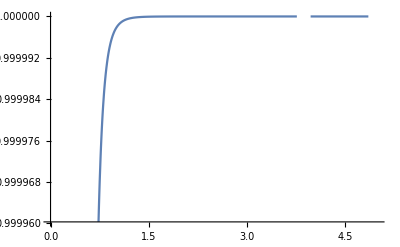

```mathematica
Plot[-((1+2 σ)^2 f[2σ]f[2σ+2])/f[2σ+1]^2,{σ,0,5}]
```

```mathematica
Plot[-σ^(1/6-4 σ^2) (1+2 σ)^(11/3+8 σ+8 σ^2) (2+2 σ)^(-23/6-8 σ-4 σ^2)2^(1/6) Sinh[4 σ^2 Log[2]]Sinh[3-1/(135168 σ^8)+1/(46080 σ^6)-1/(8064 σ^4)+1/(480 σ^2)+1/(264 (1+2 σ)^8)-1/(360 (1+2 σ)^6)+1/(252 (1+2 σ)^4)-1/(60 (1+2 σ)^2)-1/(528 (2+2 σ)^8)+1/(720 (2+2 σ)^6)-1/(504 (2+2 σ)^4)+1/(120 (2+2 σ)^2)] ,{σ,0,5}]
```

-Graphics-

```mathematica
Exp[1/4 (3-2 Log[x]) x^2-1/2 Log[2 π] x+1/12 (-1+12 Log[Glaisher]+Log[x])+1/(240 x^2)-1/(1008 x^4)+1/(1440 x^6)-1/(1056 x^8)-1/(1056 x^8)+691/(327600 x^10)-1/(144 x^12)+3617/(114240 x^14)-43867/(229824 x^16)+174611/(118800 x^18)-77683/(5520 x^20)]Exp[1/4 (3-2( Log[x]+ⅈ π)) x^2+1/2 Log[2 π] x+1/12 (-1+12 Log[Glaisher]+Log[x])+1/(240 x^2)-1/(1008 x^4)+1/(1440 x^6)-1/(1056 x^8)-1/(1056 x^8)+691/(327600 x^10)-1/(144 x^12)+3617/(114240 x^14)-43867/(229824 x^16)+174611/(118800 x^18)-77683/(5520 x^20)]//Simplify
```

ⅇ^(-1/6-77683/(2760 x^20)+174611/(59400 x^18)-43867/(114912 x^16)+3617/(57120 x^14)-1/(72 x^12)+691/(163800 x^10)-1/(264 x^8)+1/(720 x^6)-1/(504 x^4)+1/(120 x^2)+1/2 (3-ⅈ π) x^2) Glaisher^2 x^(1/6-x^2)

```mathematica
(F[{1,-1,0}]F[{0,0,0}])/(F[{1,0,0}]F[{0,-1,0}])
```

1/(1+σ1-σ2)^2

```mathematica
(Fasym[{1,-1,0}]Fasym[{0,0,0}])/(Fasym[{1,0,0}]Fasym[{0,-1,0}])//Simplify
```

ⅇ^3 (σ1-σ2)^(-(σ1-σ2)^2) (1+σ1-σ2)^(2 (1+σ1-σ2)^2) (2+σ1-σ2)^(-(2+σ1-σ2)^2)

```mathematica
Fasym[{1,0,0}]
```

ⅇ^(3/2 (1+σ1-σ2)^2+3/2 (1+σ1-σ3)^2+3/2 (σ2-σ3)^2) Glaisher^6 (1+σ1-σ2)^(-(1+σ1-σ2)^2) (1+σ1-σ3)^(-(1+σ1-σ3)^2) (σ2-σ3)^(-(σ2-σ3)^2)

```mathematica
Simplify[%55]
```

-ⅇ^((166320-105/(σ1-σ2)^8+77/(σ1-σ2)^6-110/(σ1-σ2)^4+462/(σ1-σ2)^2+210/(1+σ1-σ2)^8-154/(1+σ1-σ2)^6+220/(1+σ1-σ2)^4-924/(1+σ1-σ2)^2-105/(2+σ1-σ2)^8+77/(2+σ1-σ2)^6-110/(2+σ1-σ2)^4+462/(2+σ1-σ2)^2)/55440) (σ1-σ2)^(1/6-(σ1-σ2)^2) (1+σ1-σ2)^(-1/3+2 (1+σ1-σ2)^2) (2+σ1-σ2)^(1/6-(2+σ1-σ2)^2)

```mathematica
Series[(1+σ1-σ2)^2 ⅇ^3 (σ1-σ2)^(1/6-(σ1-σ2)^2) (1+σ1-σ2)^(-1/3+2 (1+σ1-σ2)^2) (2+σ1-σ2)^(1/6-(2+σ1-σ2)^2),{σ1,Infinity,4},{σ2,Infinity,4}]
```

1-1/(20 σ1^4)+O[1/σ1]^5

```mathematica
Series[ⅇ^3(1+σ1-σ2)^2(σ1-σ2)^(-(σ1-σ2)^2) (1+σ1-σ2)^(+2 (1+σ1-σ2)^2) (2+σ1-σ2)^(-(2+σ1-σ2)^2),{σ1,Infinity,4},{σ2,Infinity,4}]
```

1+1/(6 σ1^2)+(σ2/3-1/3+O[1/σ2]^5)/σ1^3+(σ2^2/2-σ2+197/360+O[1/σ2]^5)/σ1^4+O[1/σ1]^5

```mathematica
1 2+( 1^3(2)+ 2^3(-1))/3
```

0

```mathematica
Series[(1+x)^(-(1+x)^2)(-1+x)^(-(-1+x)^2)(x)^(2(x)^2),{x,Infinity,10}]
```

1/(ⅇ^3 x^2)+1/(6 ⅇ^3 x^4)+17/(360 ⅇ^3 x^6)+827/(45360 ⅇ^3 x^8)+46759/(5443200 ⅇ^3 x^10)+O[1/x]^11

```mathematica
(1+x)^(-(1+x)^2)(-1+x)^(-(-1+x)^2)(x)^(2(x)^2)//Simplify
```

(-1+x)^(-(-1+x)^2) x^(2 x^2) (1+x)^(-(1+x)^2)

```mathematica
ⅇ^(+3/2  x^2) x^(-x^2)/.{x->x+1}//Simplify
```

ⅇ^(3/2 (1+x)^2) (1+x)^(-(1+x)^2)

```mathematica
Exp[(-1-2 Log[x]) x+1/2 (-3-2 Log[x])]//FullSimplify
```

ⅇ^(-3/2-x) x^(-1-2 x)

```mathematica
Series[Log[1+x],{x,0,2}]
```

x-x^2/2+O[x]^3

```mathematica
((Exp[2Log[1+x]] f[x]f[x+2])/f[x+1]^2)/.f[x_]->Exp[a x^2 + b x^2 Log[x]]
```

ⅇ^(a x^2-2 a (1+x)^2+a (2+x)^2+b x^2 Log[x]-2 b (1+x)^2 Log[1+x]+b (2+x)^2 Log[2+x]) (1+x)^2

```mathematica
nx=4;
nlog = 4;
fasymp[x_]:=Sum[ Subscript[c, kx,klog] x^kx Log[x]^klog,{kx,-2,nx},{klog,0,nlog}]
```

```mathematica
fasymp[x]
```

c_(0,0)+Log[x] c_(0,1)+Log[x]^2 c_(0,2)+x c_(1,0)+x Log[x] c_(1,1)+x Log[x]^2 c_(1,2)+x^2 c_(2,0)+x^2 Log[x] c_(2,1)+x^2 Log[x]^2 c_(2,2)

f[x+1]-f[x]==Sin[x]

WolframAlphaQueryResults

f[x+1]-2 f[x]+f[x-1]== -2 Log[x]

WolframAlphaQueryResults

f[x+1]-f[x]== c-2 Log[x+1]

WolframAlphaQueryResults

```mathematica
WolframAlpha["f[x+1]-f[x]== c-2 Log[x+1]",{{"RecurrenceEquationSolution",1},"Output"}]
```

HoldComplete[{{f[x]==c x+C[1]-2 Log[Pochhammer[1,x]]}}]

f[x+1]-f[x]== -2 Log[Abs[Pochhammer[1,x]]]

WolframAlphaQueryResults

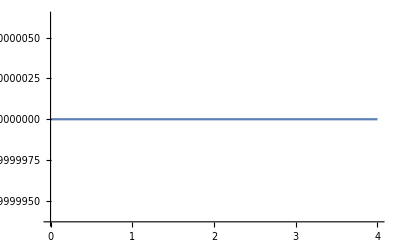

```mathematica
Plot[Exp[-2Log[BarnesG[1+x+2]]+2 2 Log[BarnesG[1+x+1]]-2Log[BarnesG[1+x]]+2Log[1+x]],{x,0,4}]
```

```mathematica
Series[Exp[-2Log[BarnesG[1+x]]],{x,Infinity,3}]//Normal//FullSimplify
```

```mathematica
(*The difference comes from the reflection formula*)
Log[BarnesG[1-x]/BarnesG[1+x]]+x Log[Sin[π x]/π]//FullSimplify
```

Log[BarnesG[1-x]/BarnesG[1+x]]+x Log[Sin[π x]/π]

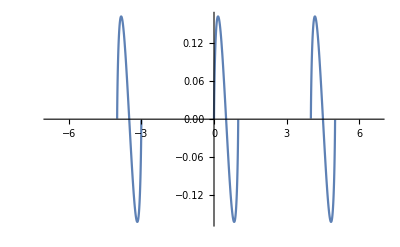

```mathematica
Plot[Log[BarnesG[1-x]/BarnesG[1+x]]-x Log[Sin[π x]/π],{x,-6.75,6.75}]
```

```mathematica
FullSimplify[((Series[Exp[-2Log[Abs[BarnesG[1+x]]]],{x,Infinity,4}]//Normal)/.{x->-x}),{x>0,x ϵ Reals}]
```

ⅇ^(-1/6-1/(504 x^4)+1/(120 x^2)+(3 x^2)/2) Glaisher^2 (2 π)^x x^(1/6-x^2)

```mathematica
FullSimplify[(Series[Exp[-Log[Abs[BarnesG[1+x]]]],{x,Infinity,4}]//Normal)((Series[Exp[-Log[Abs[BarnesG[1+x]]]],{x,Infinity,4}]//Normal)/.{x->-x}),{x>0,x ϵ Reals}]
```

ⅇ^(-1/6-1/(504 x^4)+1/(120 x^2)+(3 x^2)/2) Glaisher^2 x^(1/6-x^2)

```mathematica
FullSimplify[(Series[Exp[-Log[BarnesG[1+x]]],{x,Infinity,4}]//Normal)((Series[Exp[-Log[BarnesG[1+x]]],{x,Infinity,4}]//Normal)/.{x->-x}),{x>0,x ϵ Reals}]
```

```mathematica
ⅇ^(-1/6-1/(504 x^4)+1/(120 x^2)+1/2 (3-ⅈ π) x^2) Glaisher^2 x^(-x^2) (-x^2)^(1/12)
```

```mathematica
FullSimplify[Exp[1/2 ⅈ π x^2](Series[Exp[-Log[BarnesG[1+x]]],{x,Infinity,4}]//Normal)((Series[Exp[-Log[BarnesG[1+x]]],{x,Infinity,4}]//Normal)/.{x->-x}),{x>0,x ϵ Reals}]
```

(-1)^(1/12) ⅇ^(-1/6-1/(504 x^4)+1/(120 x^2)+(3 x^2)/2) Glaisher^2 x^(1/6-x^2)

```mathematica
Exp[3/2 x^2 - 1/2x^2 Log[x^2]]//Simplify
```

ⅇ^((3 x^2)/2) (x^2)^(-x^2/2)

```mathematica
FullSimplify[(Series[Exp[-2Log[Abs[BarnesG[1+x]]]],{x,Infinity,4}]//Normal),{x>0,x ϵ Reals}]
```

ⅇ^(-1/6-1/(504 x^4)+1/(120 x^2)+(3 x^2)/2) Glaisher^2 (2 π)^-x x^(1/6-x^2)

```mathematica
Series[FullSimplify[(Series[1/2 ⅈ π x^2-Log[BarnesG[1+x]],{x,Infinity,4}]//Normal),{x>0,x ϵ Reals}]FullSimplify[(Series[Log[BarnesG[1+x]],{x,Infinity,4}]//Normal/.{x->-x}),{x>0,x ϵ Reals}],{x,0,4}]//Simplify
```

-1/(1016064 x^8)+1/(120960 x^6)+(-221+2400 Log[Glaisher]+200 Log[x])/(1209600 x^4)-Log[2 π]/(1008 x^3)+(ⅈ (-22 ⅈ+5 π+84 ⅈ Log[Glaisher]+17 ⅈ Log[x]))/(10080 x^2)+Log[2 π]/(240 x)+(-19-3 ⅈ π+240 Log[Glaisher]-1440 Log[Glaisher]^2+(26-240 Log[Glaisher]) Log[x]-10 Log[x]^2)/1440+1/12 Log[2 π] (-1+12 Log[Glaisher]+Log[x]) x+1/24 (3-36 Log[Glaisher]-ⅈ π (-1+12 Log[Glaisher])-6 Log[2 π]^2+(-5-ⅈ π+24 Log[Glaisher]) Log[x]+2 Log[x]^2) x^2+1/4 Log[2 π] (3+ⅈ π-2 Log[x]) x^3+1/16 (3+2 ⅈ π-2 Log[x]) (-3+2 Log[x]) x^4+O[x]^5

```mathematica
FullSimplify[(Series[Log[BarnesG[1+x]],{x,Infinity,4}]//Normal/.{x->-x}),{x>0,x ϵ Reals}]
```

1/12+(5-21 (x^2+180 x^6))/(5040 x^4)-Log[Glaisher]+1/2 x Log[2 π]+1/12 (-1+6 x^2) Log[x]

```mathematica
FullSimplify[( Series[Exp[-Log[BarnesG[1+x]]],{x,Infinity,4}]//Normal)((Series[Exp[-Log[BarnesG[1+x]]],{x,Infinity,4}]//Normal)/.{x->-x}),{x>0,x ϵ Reals}]
```

(-1)^(1/12) ⅇ^(-1/6-1/(504 x^4)+1/(120 x^2)+(3 x^2)/2) Glaisher^2 x^(1/6-x^2)

```mathematica
FullSimplify[(Series[ⅇ^(1/2 ⅈ π x^2)/BarnesG[1+x],{x,Infinity,0}]//Normal)((Series[1/BarnesG[1+x],{x,Infinity,0}]//Normal)/.{x->-x}),{x>0,x ϵ Reals}]
```

(-1)^(1/12) ⅇ^(-1/6+(3 x^2)/2) Glaisher^2 x^(1/6-x^2)

```mathematica
FullSimplify[Log[(-1)^(1/12) ⅇ^(-1/6-1/(504 x^4)+1/(120 x^2)+(3 x^2)/2) Glaisher^2 x^(1/6-x^2)],{x>0,x ϵ Reals}]
```

-1/6+(ⅈ π)/12-1/(504 x^4)+1/(120 x^2)+(3 x^2)/2+2 Log[Glaisher]+(1/6-x^2) Log[x]

```mathematica
Series[-1/6+(ⅈ π)/12-1/(504 x^4)+1/(120 x^2)+(3 x^2)/2+2 Log[Glaisher]+(1/6-x^2) Log[x],{x,Infinity,4}]
```

1/2 (3-2 Log[x]) x^2+1/12 ⅈ (2 ⅈ+π-24 ⅈ Log[Glaisher]-2 ⅈ Log[x])+1/(120 x^2)-1/(504 x^4)+O[1/x]^5

```mathematica
FullSimplify[(ⅇ^(1/4 ⅈ π x^2)Series[Exp[-Log[BarnesG[1+x]]],{x,Infinity,4}]//Normal),{x>0,x ϵ Reals}]
```

ⅇ^((-420-5/x^4+21/x^2+1260 x^2 (3+ⅈ π-2 Log[x]))/5040) Glaisher (2 π)^(-x/2) x^(1/12)

```mathematica
FullSimplify[(ⅇ^(1/4 ⅈ π x^2)Series[Exp[-Log[BarnesG[1+x]]],{x,Infinity,4}]//Normal)/.{x->-x},{x>0,x ϵ Reals}]
```

ⅇ^((-420-5/x^4+21/x^2+1260 (3-ⅈ π) x^2)/5040) Glaisher (2 π)^(x/2) (-x)^(1/12) x^(-x^2/2)

```mathematica
ⅇ^((-420-5/x^4+21/x^2+1260 (3-ⅈ π) x^2)/5040) Glaisher (2 π)^(x/2) (-x)^(1/12) x^(-x^2/2)ⅇ^((-420-5/x^4+21/x^2+1260 x^2 (3+ⅈ π-2 Log[x]))/5040) Glaisher (2 π)^(-x/2) x^(1/12)//Simplify
```

ⅇ^(-1/6-1/(504 x^4)+1/(120 x^2)+(3 x^2)/2) Glaisher^2 x^(-x^2) (-x^2)^(1/12)

```mathematica
Simplify[ⅇ^(1/2 ⅈ π x^2)ⅇ^(-1/6-1/(504 x^4)+1/(120 x^2)+1/2 (3-ⅈ π) x^2) Glaisher^2 x^(-x^2) (-x^2)^(1/12),x^2>0]
```

ⅇ^(-1/6-1/(504 x^4)+1/(120 x^2)+(3 x^2)/2) Glaisher^2 x^(-x^2) (-x^2)^(1/12)

```mathematica
ⅇ^(-1/6-1/(504 x^4)+1/(120 x^2)+(3 x^2)/2) Glaisher^2 x^(1/6-x^2)/.{x->I x}//Simplify
```

ⅇ^(-1/6-1/(504 x^4)-1/(120 x^2)-(3 x^2)/2) Glaisher^2 (ⅈ x)^(1/6+x^2)

```mathematica
ⅇ^(-1/6-1/(504 x^4)+1/(120 x^2)+1/2 (3-ⅈ π) x^2) Glaisher^2 x^(-x^2) (-x^2)^(1/12)/(ⅇ^(-1/6-1/(504 x^4)-1/(120 x^2)-(3 x^2)/2) Glaisher^2 (ⅈ x)^(1/6+x^2))/.{x->4}//Simplify
```

ⅇ^(46081/960)/18446744073709551616

```mathematica
Factor[(-1)^(1/12)]
```

(-1)^(1/12)

(-1)^(1/12)

WolframAlphaQueryResults

```mathematica
Re[(-1)^(1/12)]
```

(1+√3)/(2 √2)

```mathematica
Series[Exp[-2Log[BarnesG[1+x]]],{x,0,4}]//Simplify
```

1+(1-Log[2 π]) x+1/2 (3+2 EulerGamma-2 Log[2 π]+Log[2 π]^2) x^2+(EulerGamma-π^2/9-EulerGamma Log[2 π]+1/6 (7-9 Log[2 π]+3 Log[2 π]^2-Log[2 π]^3)) x^3+1/72 (36 EulerGamma^2+8 π^2 (-1+Log[2 π])+36 EulerGamma (3-2 Log[2 π]+Log[2 π]^2)+3 (25-28 Log[2 π]+18 Log[2 π]^2-4 Log[2 π]^3+Log[2 π]^4+12 Zeta[3])) x^4+O[x]^5

```mathematica
(Series[Exp[-2Log[BarnesG[1+x]]],{x,0,4}]//Simplify)-(Series[Exp[-Log[BarnesG[1+x]]],{x,0,4}]((Series[Exp[-Log[BarnesG[1+x]]],{x,0,4}]//Normal)/.{x->-x})//Simplify)
```

(1-Log[2 π]) x+(-1-EulerGamma+1/2 (3+2 EulerGamma-2 Log[2 π]+Log[2 π]^2)) x^2+(EulerGamma-π^2/9-EulerGamma Log[2 π]+1/6 (7-9 Log[2 π]+3 Log[2 π]^2-Log[2 π]^3)) x^3+(1/2 (-1-2 EulerGamma-EulerGamma^2-Zeta[3])+1/72 (36 EulerGamma^2+8 π^2 (-1+Log[2 π])+36 EulerGamma (3-2 Log[2 π]+Log[2 π]^2)+3 (25-28 Log[2 π]+18 Log[2 π]^2-4 Log[2 π]^3+Log[2 π]^4+12 Zeta[3]))) x^4+O[x]^5

```mathematica
Series[Exp[-Log[BarnesG[1+x]]],{x,0,4}]
```

1+(1/2-1/2 Log[2 π]) x+1/8 (5+4 EulerGamma-2 Log[2 π]+Log[2 π]^2) x^2+1/144 (39+36 EulerGamma-8 π^2-45 Log[2 π]-36 EulerGamma Log[2 π]+9 Log[2 π]^2-3 Log[2 π]^3) x^3+1/1152(219+360 EulerGamma+144 EulerGamma^2-32 π^2-156 Log[2 π]-144 EulerGamma Log[2 π]+32 π^2 Log[2 π]+90 Log[2 π]^2+72 EulerGamma Log[2 π]^2-12 Log[2 π]^3+3 Log[2 π]^4+288 Zeta[3]) x^4+O[x]^5

```mathematica
Series[Exp[-Log[BarnesG[1+x]]],{x,0,4}](Series[Exp[-Log[BarnesG[1+x]]],{x,0,4}]//Normal/.{x->-x})//Simplify
```

1+(1-Log[2 π]) x+1/2 (3+2 EulerGamma-2 Log[2 π]+Log[2 π]^2) x^2+(EulerGamma-π^2/9-EulerGamma Log[2 π]+1/6 (7-9 Log[2 π]+3 Log[2 π]^2-Log[2 π]^3)) x^3+1/72 (36 EulerGamma^2+8 π^2 (-1+Log[2 π])+36 EulerGamma (3-2 Log[2 π]+Log[2 π]^2)+3 (25-28 Log[2 π]+18 Log[2 π]^2-4 Log[2 π]^3+Log[2 π]^4+12 Zeta[3])) x^4+O[x]^5

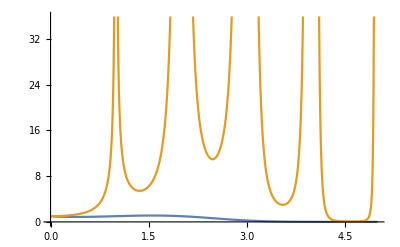

```mathematica
Plot[{Exp[-2Log[BarnesG[1+x]]],Abs[Exp[-Log[BarnesG[1+x]]]Exp[-Log[BarnesG[1-x]]]]},{x,0,5}]
```

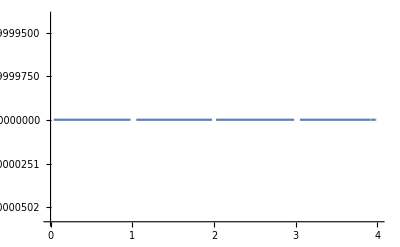

```mathematica
Plot[Exp[-1Log[BarnesG[1-x-2]BarnesG[1+x+2]]+2 Log[BarnesG[1-x-1]BarnesG[1+x+1]]-1Log[BarnesG[1-x]BarnesG[1+x]]+2Log[1+x]],{x,0,4}]
```

```mathematica
Abs[Exp[-1Log[BarnesG[1-x-2]BarnesG[1+x+2]]+2 Log[BarnesG[1-x-1]BarnesG[1+x+1]]-1Log[BarnesG[1-x]BarnesG[1+x]]]]-2Log[1+x]//Simplify
```

Abs[(BarnesG[-x]^2 BarnesG[2+x]^2)/(BarnesG[-1-x] BarnesG[1-x] BarnesG[1+x] BarnesG[3+x])]-2 Log[1+x]

```mathematica
Abs[(BarnesG[-x]^2 BarnesG[2+x]^2)/(BarnesG[-1-x] BarnesG[1-x] BarnesG[1+x] BarnesG[3+x])](1+x)^2
```

```mathematica
(BarnesG[-x]^2 BarnesG[2+x]^2)/(BarnesG[-1-x] BarnesG[1-x] BarnesG[1+x] BarnesG[3+x])
```

```mathematica
y^2 D[y^(-1)H[y]+H[0]+H[y],y]//Simplify
```

-H[y]+y (1+y) H'[y]

```mathematica
Sum
```

```mathematica
RSolve[f[x+1]- f[x]==-2 Log[Abs[x]],f[x],x]
```

{{f[x]→C[1]+(Piecewise[{{0, Global`K$10732168-x==-1&&Global`K$10732168<0&&x<1}, {-2 ⅈ π, (Global`K$10732168==0&&x==1)||(Global`K$10732168>0&&Global`K$10732168-x==-1)}, {-2 Log[Pochhammer[-1,Floor[x]]], Global`K$10732168==0&&x>1}, {-2 Log[Pochhammer[-1,Floor[-Global`K$10732168+x]]], Global`K$10732168>0&&Global`K$10732168-x<-1}, {-2 (Log[Pochhammer[-1+Ceiling[-Global`K$10732168],1-Ceiling[-Global`K$10732168]+Floor[-Global`K$10732168]]]-LogGamma[2-Ceiling[-Global`K$10732168]]), x==1&&Global`K$10732168<0}, {-2 (Log[Pochhammer[-1+Ceiling[-Global`K$10732168],-Ceiling[-Global`K$10732168]+Floor[-Global`K$10732168+x]]]-LogGamma[2-Ceiling[-Global`K$10732168]]), Global`K$10732168<0&&x>1}, {2 LogGamma[2-Floor[-Global`K$10732168+x]], Global`K$10732168<0&&Global`K$10732168-x<-1&&x<1}, {0, True}}])}}

```mathematica
Log[Gamma[1+x]/Gamma[x]]
```

Log[Gamma[1+x]/Gamma[x]]

```mathematica
FullSimplify[2Log[Gamma[1+x]/Gamma[x]]]
```

2 Log[x]

```mathematica
FullSimplify[Log[(Gamma[1+α (x+1)]Gamma[1+β (x+1)])/(Gamma[1+α (x)]Gamma[1+β (x)])]/.{α->1,β->-1}]
```

Log[-(1+x)/x]

```mathematica
Series[Zeta[-s,1+x],{x,0,3}]
```

Zeta[-s]+s Zeta[1-s] x+1/2 (-1+s) s Zeta[2-s] x^2+1/6 (-2+s) (-1+s) s Zeta[3-s] x^3+O[x]^4

```mathematica
D[(k+x)^(-s),s]
```

-(k+x)^-s Log[k+x]

```mathematica
x Log[Pochhammer[1,x]]
```

x Log[Pochhammer[1,x]]

```mathematica
Solve[1/y(F[y]-F[0])-F'[0]-2F[y]+2F[0]+y F[y]==h[y],F[y]]//Simplify
```

{{F[y]→(F[0]-2 y F[0]+y h[y]+y F'[0])/(-1+y)^2}}

```mathematica
Series[Derivative[1,0][Zeta][-1,1+x],{x,0,3}]
```

Zeta^(1,0)[-1,1]+Zeta^(1,1)[-1,1] x+1/2 Zeta^(1,2)[-1,1] x^2+1/6 Zeta^(1,3)[-1,1] x^3+O[x]^4

```mathematica
RSolve[f[x+2]-2f[x+1]+f[x]==-2 Log[Abs[1+x]],f[x],x]
```

$Aborted

```mathematica
Log[Abs[Gamma[1+x+1]]]-Log[Abs[Gamma[1+x]]]
```

-Log[Abs[Gamma[1+x]]]+Log[Abs[Gamma[2+x]]]

```mathematica
Simplify[-Log[Abs[Gamma[1+x]]]+Log[Abs[Gamma[2+x]]]]
```

Log[Abs[Gamma[2+x]]/Abs[Gamma[1+x]]]

```mathematica
Simplify[-Log[Abs[Gamma[1-x] Gamma[1+x]]]+Log[Abs[Gamma[-x] Gamma[2+x]]]]
```

Log[Abs[Gamma[-x] Gamma[2+x]]/Abs[Gamma[1-x] Gamma[1+x]]]

```mathematica
FullSimplify[Abs[Gamma[-x] Gamma[2+x]]/Abs[Gamma[1-x] Gamma[1+x]]]
```

Abs[1+1/x]

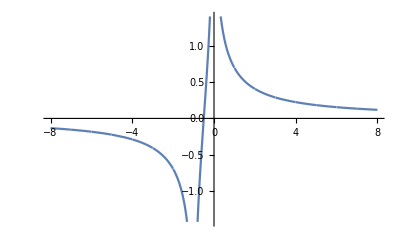

```mathematica
Plot[Log[Abs[Gamma[-x] Gamma[2+x]]/Abs[Gamma[1-x] Gamma[1+x]]],{x,-8,8}]
```

```mathematica
FullSimplify[-Log[Gamma[1-x] Gamma[1+x]]+Log[Gamma[-x] Gamma[2+x]]]
```

-Log[x Csc[π x]]+Log[-(1+x) Csc[π x]]

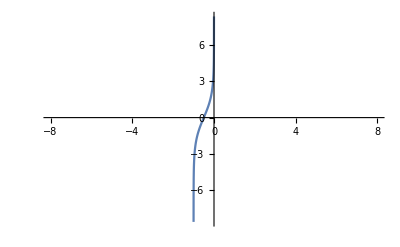

```mathematica
Plot[-Log[x Csc[π x]]+Log[-(1+x) Csc[π x]],{x,-8,8}]
```

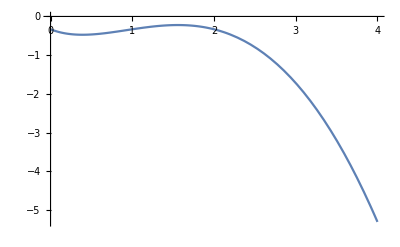

```mathematica
Plot[-2 (x Log[Pochhammer[1,x]]-Derivative[1,0][Zeta][-1,1+x]),{x,0,4}]
```

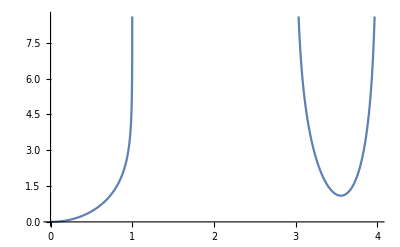

```mathematica
Plot[-1Log[BarnesG[1+x]BarnesG[1-x]],{x,0,4}]
```

```mathematica
(BarnesG[1+x+1]BarnesG[1-x-1])^2/((BarnesG[1+x+2]BarnesG[1-x-2])(BarnesG[1+x]BarnesG[1-x]))
```

(BarnesG[-x]^2 BarnesG[2+x]^2)/(BarnesG[-1-x] BarnesG[1-x] BarnesG[1+x] BarnesG[3+x])

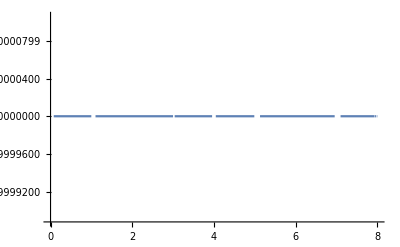

```mathematica
Plot[Abs[(BarnesG[-x]^2 BarnesG[2+x]^2)/(BarnesG[-1-x] BarnesG[1-x] BarnesG[1+x] BarnesG[3+x])](1+x)^2,{x,0,8}]
```

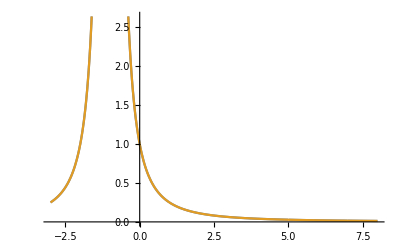

```mathematica
Plot[{Abs[(BarnesG[-x]^2 BarnesG[2+x]^2)/(BarnesG[-1-x] BarnesG[1-x] BarnesG[1+x] BarnesG[3+x])],1/(1+x)^2},{x,-3,8}]
```

```mathematica
fg[xExp[Log[BarnesG[1+x]BarnesG[1-x]]]
```

```mathematica
RSolve[f[x+1]-f[x]==2 Log[Pochhammer[1,x]],f[x],x]
```

{{f[x]→C[1]+2 Log[BarnesG[1+x]]}}

```mathematica
Integrate[ Exp[x],{x,0,1}]
```

-1+ⅇ

```mathematica
RSolve[f[x+1]-f[x]==-2 Log[1+x],f[x],x]
```

{{f[x]→C[1]-2 Log[Pochhammer[1,x]]}}

```mathematica
f[x+1]-f[x]/.{f[x_]->Log[Abs[Gamma[x]Gamma[-x]]]}//FullSimplify
```

Log[Abs[x/(1+x)]]

```mathematica
Gamma[2+x]/Gamma[1+x]
```

Gamma[2+x]/Gamma[1+x]

BarnesG[2+x]/BarnesG[1+x]

```mathematica
Sum[k y^k Log[x+k+1],{k,0,Infinity}]
```

∑_(k=0)^∞ k y^k Log[1+k+x]

```mathematica
f[x+2]-2f[x+1]+f[x]/.{f[x_]->g[x](a x+ b)}
```

(b+a x) g[x]-2 (b+a (1+x)) g[1+x]+(b+a (2+x)) g[2+x]

```mathematica
Simplify[(b+a x) g[x]-2 (b+a (1+x)) g[1+x]+(b+a (2+x)) g[2+x]]
```

(b+a x) g[x]-2 (a+b+a x) g[1+x]+(b+a (2+x)) g[2+x]

```mathematica
(b+a x) g[x]-2 (b+a (1+x)) g[1+x]+(b+a (2+x)) g[1+x]//Simplify
```

(b+a x) (g[x]-g[1+x])

```mathematica
(b+a (-1+x)) g[-1+x]-2 (b+a x) g[x]+(b+a (1+x)) g[1+x]//Expand
```

-a g[-1+x]+b g[-1+x]+a x g[-1+x]-2 b g[x]-2 a x g[x]+a g[1+x]+b g[1+x]+a x g[1+x]

```mathematica
-Derivative[0,1,0][LerchPhi][y,0,x]
```

```mathematica
Solve[F==f[x]+y f[x+1]+y Z,{Z}]
```

{{Z→(F-f[x]-y f[1+x])/y}}

```mathematica
D[Sum[y^k f[x+k],{k,0,3}],y]
```

f[1+x]+2 y f[2+x]+3 y^2 f[3+x]

```mathematica
1/y(Sum[y^k f[x+k],{k,0,3}]-(Sum[y^k f[x+k],{k,0,3}]/.y->0))-(D[Sum[y^k f[x+k],{k,0,3}],y]/.y->0)//Expand
```

y f[2+x]+y^2 f[3+x]

```mathematica
Sum[y^k f[x+k+1],{k,1,3}]//Expand
```

y f[2+x]+y^2 f[3+x]+y^3 f[4+x]

```mathematica
Series[fasymp[x+1]-2fasymp[x]+fasymp[x-1],{x,Infinity,2}]/.{}//Simplify
```

(12 c_(4,0)+(7+12 Log[x]) c_(4,1)+2 c_(4,2)+14 Log[x] c_(4,2)+12 Log[x]^2 c_(4,2)+6 Log[x] c_(4,3)+21 Log[x]^2 c_(4,3)+12 Log[x]^3 c_(4,3)+12 Log[x]^2 c_(4,4)+28 Log[x]^3 c_(4,4)+12 Log[x]^4 c_(4,4)) x^2+(6 c_(3,0)+(5+6 Log[x]) c_(3,1)+2 c_(3,2)+10 Log[x] c_(3,2)+6 Log[x]^2 c_(3,2)+6 Log[x] c_(3,3)+15 Log[x]^2 c_(3,3)+6 Log[x]^3 c_(3,3)+12 Log[x]^2 c_(3,4)+20 Log[x]^3 c_(3,4)+6 Log[x]^4 c_(3,4)) x+(2 c_(2,0)+(3+2 Log[x]) c_(2,1)+2 c_(2,2)+6 Log[x] c_(2,2)+2 Log[x]^2 c_(2,2)+6 Log[x] c_(2,3)+9 Log[x]^2 c_(2,3)+2 Log[x]^3 c_(2,3)+12 Log[x]^2 c_(2,4)+12 Log[x]^3 c_(2,4)+2 Log[x]^4 c_(2,4)+2 c_(4,0)+(25 c_(4,1))/6+2 Log[x] c_(4,1)+(35 c_(4,2))/6+25/3 Log[x] c_(4,2)+2 Log[x]^2 c_(4,2)+5 c_(4,3)+35/2 Log[x] c_(4,3)+25/2 Log[x]^2 c_(4,3)+2 Log[x]^3 c_(4,3)+2 c_(4,4)+20 Log[x] c_(4,4)+35 Log[x]^2 c_(4,4)+50/3 Log[x]^3 c_(4,4)+2 Log[x]^4 c_(4,4))+1/x(c_(1,1)+2 (1+Log[x]) c_(1,2)+6 Log[x] c_(1,3)+3 Log[x]^2 c_(1,3)+12 Log[x]^2 c_(1,4)+4 Log[x]^3 c_(1,4)+(c_(3,1))/2+(11 c_(3,2))/6+Log[x] c_(3,2)+3 c_(3,3)+11/2 Log[x] c_(3,3)+3/2 Log[x]^2 c_(3,3)+2 c_(3,4)+12 Log[x] c_(3,4)+11 Log[x]^2 c_(3,4)+2 Log[x]^3 c_(3,4))+1/x^2(-c_(0,1)-2 (-1+Log[x]) c_(0,2)+6 Log[x] c_(0,3)-3 Log[x]^2 c_(0,3)+12 Log[x]^2 c_(0,4)-4 Log[x]^3 c_(0,4)-(c_(2,1))/6-(c_(2,2))/6-1/3 Log[x] c_(2,2)+c_(2,3)-1/2 Log[x] c_(2,3)-1/2 Log[x]^2 c_(2,3)+2 c_(2,4)+4 Log[x] c_(2,4)-Log[x]^2 c_(2,4)-2/3 Log[x]^3 c_(2,4)-(c_(4,1))/15-(13 c_(4,2))/90-2/15 Log[x] c_(4,2)+(c_(4,3))/4-13/30 Log[x] c_(4,3)-1/5 Log[x]^2 c_(4,3)+(5 c_(4,4))/3+Log[x] c_(4,4)-13/15 Log[x]^2 c_(4,4)-4/15 Log[x]^3 c_(4,4))+O[1/x]^3

```mathematica
(x+1)^2-x^2+(x-1)^2//Expand
```

2+x^2

```mathematica
D[g[x+1],x]
```

g'[1+x]

```mathematica
Series[fasymp[x+1]-2fasymp[x]+fasymp[x-1],{x,Infinity,2}]/.{Subscript[c, 2,2]->0,Subscript[c, 2,1]->-1,Subscript[c, 2,0]->3/2}
```

(-2 Log[x]^4+2 c_(2,-1)-3 Log[x] c_(2,-1)+2 Log[x]^2 c_(2,-1))/Log[x]^3+(2 c_(1,-1)-Log[x] c_(1,-1)+Log[x]^3 c_(1,1)+2 Log[x]^3 c_(1,2)+2 Log[x]^4 c_(1,2))/(Log[x]^3 x)+(Log[x]^5+12 Log[x]^2 c_(0,-1)+6 Log[x]^3 c_(0,-1)-6 Log[x]^5 c_(0,1)+12 Log[x]^5 c_(0,2)-12 Log[x]^6 c_(0,2)+12 c_(2,-1)-6 Log[x] c_(2,-1)-Log[x]^2 c_(2,-1)+Log[x]^3 c_(2,-1))/(6 Log[x]^5 x^2)+O[1/x]^3

```mathematica
Series[a x^2-2 a (1+x)^2+a (2+x)^2+b x^2 Log[x]-2 b (1+x)^2 Log[1+x]+b (2+x)^2 Log[2+x]+2Log[1+x],{x,Infinity,3}]/.{b->-1}
```

(-3+2 a)+1/(6 x^2)-1/(3 x^3)+O[1/x]^4

```mathematica
Series[a x^2-2 a (1+x)^2+a (2+x)^2+b x^2 Log[x]-2 b (1+x)^2 Log[1+x]+b (2+x)^2 Log[2+x]+2Log[1+x],{x,Infinity,3}]/.{b->-1}
```

$Aborted

```mathematica
Series[1/(BarnesG[1+x]BarnesG[1-x]),{x,0,5}]
```

1+(1+EulerGamma) x^2+1/2 (1+2 EulerGamma+EulerGamma^2+Zeta[3]) x^4+O[x]^6

```mathematica
Clear[f]
```

```mathematica
Series[-2Log[x+1],{x,Infinity,1}]
```

-2 Log[x]-2/x+O[1/x]^2

```mathematica
Series[(x+k)^n(Log[x+k])^m,{k,0,3}]//Normal
```

x^n Log[x]^m+k x^(-1+n) Log[x]^(-1+m) (m+n Log[x])+1/2 k^2 x^(-2+n) Log[x]^(-2+m) (-m+m^2-m Log[x]+2 m n Log[x]-n Log[x]^2+n^2 Log[x]^2)+1/6 k^3 x^(-3+n) Log[x]^(-3+m) (2 m-3 m^2+m^3+3 m Log[x]-3 m^2 Log[x]-3 m n Log[x]+3 m^2 n Log[x]+2 m Log[x]^2-6 m n Log[x]^2+3 m n^2 Log[x]^2+2 n Log[x]^3-3 n^2 Log[x]^3+n^3 Log[x]^3)

```mathematica
f[x_,k_]:=x^n Log[x]^m+k x^(-1+n) Log[x]^(-1+m) (m+n Log[x])+1/2 k^2 x^(-2+n) Log[x]^(-2+m) (-m+m^2-m Log[x]+2 m n Log[x]-n Log[x]^2+n^2 Log[x]^2)+1/6 k^3 x^(-3+n) Log[x]^(-3+m) (2 m-3 m^2+m^3+3 m Log[x]-3 m^2 Log[x]-3 m n Log[x]+3 m^2 n Log[x]+2 m Log[x]^2-6 m n Log[x]^2+3 m n^2 Log[x]^2+2 n Log[x]^3-3 n^2 Log[x]^3+n^3 Log[x]^3)
```

```mathematica
Apart[3/2(f[x,2]-2f[x,1]+f[x,0]//Simplify)/.{m->0,n->2},x]
```

3

```mathematica
Apart[-(f[x,2]-2f[x,1]+f[x,0]//Simplify)/.{m->1,n->2},x]//Simplify
```

-3-2/x-2 Log[x]

```mathematica
3/2(f[x,0]/.{m->0,n->2})-(f[x,0]/.{m->1,n->2})
```

(3 x^2)/2-x^2 Log[x]

```mathematica
((1+x)^2 f[x]f[x+2])/f[x+1]^2/.f[x_]->(Λ^(x^2-x)s[x])/(G[(1+ x)]G[(1- x)])//Simplify
```

-(Λ^2 s[x] s[2+x])/s[1+x]^2

```mathematica
((x/Λ)^2 f[x-1]f[x+1])/f[x]^2/.f[x_]->(Λ^(x^2-x)1)/(G[1+ I x]G[1-I x])//Simplify
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -ⅈ x.

Hold[Simplify[((x/Λ)^2 f[x-1] f[x+1])/f[x]^2/.f[x_]→(Λ^(x^2-x))/(G[1+ⅈ x] G[1-ⅈ x])]]

```mathematica
f[x-1]/.f[x_]->(Λ^(x^2-x)s[x])/(G[(1+ x)]G[(1- x)])//Simplify
```

-(Λ^(2-3 x+x^2) s[-1+x])/(x G[-x] G[x] Γ[-x]^2)

```mathematica
(x/Λ)^2 f[x-1]f[x+1]/.f[x_]->(Λ^(x^2-x))/(G[1+  x]G[1-  x])//Simplify
```

-Λ^(2 (-1+x) x)/(G[-x]^2 G[x]^2 Γ[-x]^2 Γ[x]^2)

```mathematica
((x)^2 f[x+1]f[x-1])/f[x]^2/.f[x_]->(Λ^(x^2-x))/(G[1+  x]G[1-  x])//Simplify
```

-Λ^2

```mathematica
(f[x+1]f[x-1])/f[x]^2/.f[x_]->(Λ^(x^2-x))/(G[1+  x]G[1-  x])/.x->I x//Simplify
```

Λ^2/x^2

```mathematica
RSolve[(x)^2 f[x-1]f[x+1]==f[x]^2,f[x],x]
```

{{f[x]→ⅇ^(C[1]+x C[2]-2 (x Log[Pochhammer[1,x]]-Zeta^(1,0)[-1,1+x]))}}

```mathematica
ⅇ^(-2 (x Log[Pochhammer[1,x]]-Derivative[1,0][Zeta][-1,1+x]))
```

ⅇ^(-2 (x Log[Pochhammer[1,x]]-Zeta^(1,0)[-1,1+x]))

```mathematica
Simplify[ⅇ^(-2 (x Log[Pochhammer[1,x]]-Derivative[1,0][Zeta][-1,1+x]))]
```

ⅇ^(2 Zeta^(1,0)[-1,1+x]) Pochhammer[1,x]^(-2 x)

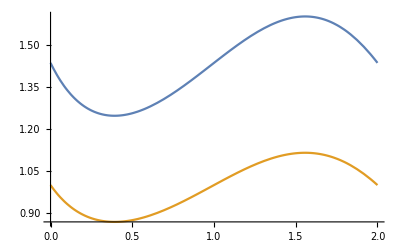

```mathematica
Plot[{2 ⅇ^(2 Derivative[1,0][Zeta][-1,1+x]) Pochhammer[1,x]^(-2 x),1/BarnesG[1+x]^2},{x,0,2}]
```

```mathematica
G[1+ x]/G[x]
```

Γ[x]

```mathematica
RSolve[h[x]/h[x-1]==L^x,h[x],x]
```

$Aborted

```mathematica
1/2 (-2+x+x^2)//Simplify
```

1/2 (-2+x+x^2)

```mathematica
h[x]/h[x-1]/.h[x_]->1/Γ[x+1]
```

1/x

```mathematica
((x)^2 f[x-1]f[x+1])/f[x]^2/.f[x_]->ⅇ^(2 Derivative[1,0][Zeta][-1,1+x]) Pochhammer[1,x]^(-2 x)//Simplify
```

ⅇ^(2 (Zeta^(1,0)[-1,x]-2 Zeta^(1,0)[-1,1+x]+Zeta^(1,0)[-1,2+x])) x^2 Pochhammer[1,-1+x]^(2-2 x) Pochhammer[1,x]^(4 x) Pochhammer[1,1+x]^(-2 (1+x))

```mathematica
Simplify[(x^2 BarnesG[1-x]^2 BarnesG[1+x]^2)/(BarnesG[2-x] BarnesG[-x] BarnesG[x] BarnesG[2+x]),{xϵ Reals}]
```

(x^2 BarnesG[1-x]^2 BarnesG[1+x]^2)/(BarnesG[2-x] BarnesG[-x] BarnesG[x] BarnesG[2+x])

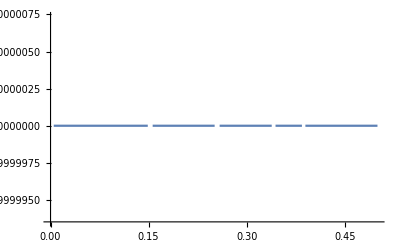

```mathematica
Plot[ⅇ^(2 (Derivative[1,0][Zeta][-1,x]-2 Derivative[1,0][Zeta][-1,1+x]+Derivative[1,0][Zeta][-1,2+x])) x^2 Pochhammer[1,-1+x]^(2-2 x) Pochhammer[1,x]^(4 x) Pochhammer[1,1+x]^(-2 (1+x)),{x,0,1/2}]
```

```mathematica
G[1+x]
```

G[x] Γ[x]

```mathematica
ⅇ^(1/2 ⅈ (-π x+π x^2))//Simplify
```

ⅇ^(1/2 ⅈ π (-1+x) x)

```mathematica
Simplify[((1+x) h[x] h[2+x])/((-1-x) h[1+x]^2)]
```

```mathematica
RSolve[-h[x] h[2+x]==h[1+x]^2,h[x],x]
```

{{h[x]→ⅇ^(1/2 ⅈ (-π x+π x^2)+C[1]+x C[2])}}

-((h[x]*h[2 + x])/h[1 + x]^2)

$Aborted

```mathematica
Simplify[((1+x)^2 G[ⅈ-ⅈ (1+x)]^2 G[ⅈ+ⅈ (1+x)]^2)/(G[ⅈ-ⅈ x] G[ⅈ+ⅈ x] G[ⅈ-ⅈ (2+x)] G[ⅈ+ⅈ (2+x)])]
```

((1+x)^2 G[2 ⅈ+ⅈ x]^2 G[-ⅈ x]^2)/(G[-ⅈ-ⅈ x] G[ⅈ-ⅈ x] G[ⅈ+ⅈ x] G[3 ⅈ+ⅈ x])

```mathematica
Simplify[((1+x)^2 BarnesG[1-ⅈ (1+x)]^2 BarnesG[1+ⅈ (1+x)]^2)/(BarnesG[1-ⅈ x] BarnesG[1+ⅈ x] BarnesG[1-ⅈ (2+x)] BarnesG[1+ⅈ (2+x)])]
```

((1+x)^2 BarnesG[(1+ⅈ)+ⅈ x]^2 BarnesG[-ⅈ ((1+ⅈ)+x)]^2)/(BarnesG[1-ⅈ x] BarnesG[1+ⅈ x] BarnesG[(1+2 ⅈ)+ⅈ x] BarnesG[-ⅈ ((2+ⅈ)+x)])

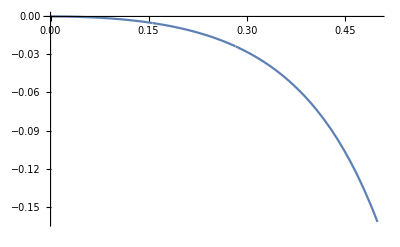

```mathematica
Plot[Im[((1+I x)^2 BarnesG[-ⅈ x]^2 BarnesG[ⅈ (2+x)]^2)/(BarnesG[ⅈ (-1-x)] BarnesG[ⅈ (1-x)] BarnesG[ⅈ (1+x)] BarnesG[ⅈ (3+x)])],{x,0,1/2}]
```